# Leads connected to 1 - 10 and 1 to 10

# a1 and a2

```mathematica
Clear[β]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[20]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[10]
```

{{{0.-0.848911 ⅈ,0.499585+0. ⅈ,0.+0.170328 ⅈ,0.00145614+0. ⅈ,0.+0.0215636 ⅈ,-0.00305462+0. ⅈ,0.+0.0108578 ⅈ,0.00416569+0. ⅈ,0.-0.000257949 ⅈ,-0.00451733+0. ⅈ},8,{-0.00451733+0. ⅈ,0.-0.000257949 ⅈ,0.00416569+0. ⅈ,0.+0.0108578 ⅈ,-0.00305462+0. ⅈ,0.+0.0215636 ⅈ,0.00145614+0. ⅈ,0.+0.170328 ⅈ,0.499585+0. ⅈ,0.-0.848911 ⅈ}},248,{{0.497586-0.230577 ⅈ,-0.128014+0.288378 ⅈ,7,0.0119669-0.0352477 ⅈ},8,{0.0119669-1,8,1}}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T[1,20]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

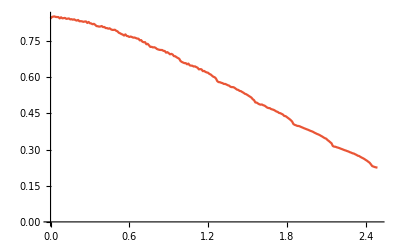

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,20][[1,1]]]},{ω,Range[0,2.5,0.01]}]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,20,1,10]],concentration],RandomSample[Join[s[1,20,11,20]],total-concentration]],First],1000]
```

```mathematica
ListPlot[{Join[s[1,20,1,20]],dist[60,25][[RandomInteger[{1,1000}]]]},PlotMarkers->Automatic,PlotStyle->{Green,Black}]
```

```mathematica
TLD[t_]:=Module[{},Module[{mat=RandomInteger[0,{20,20}]},ReplacePart[mat,Table[{a,a},{a,1,10}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[20]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[20]},MAT[[1;;10,1;;10]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Inverse[IdentityMatrix[20]-g[ω,0.0001,1,0,20].T[1,20].SLLEAD[ω,20].T[1,20]].g[ω,0.0001,1,0,20]
```

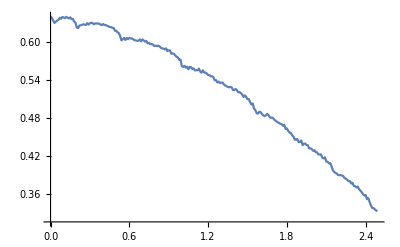

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω][[11,11]]]},{ω,Range[0,2.49,0.01]}]]
```

```mathematica
Clear[CA]
```

```mathematica
F[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Module[{J=β[ω,δ,t,ϵ,20],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J=J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[20]-Inverse[Module[{J=β[ω,δ,t,ϵ,20]},Do[J=Module[{m=unitcell},If[dist[total,concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration][[number]][[loc1,2]],dist[total,concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,20].J1.T[1,20]].Inverse[Module[{J=β[ω,δ,t,ϵ,20]},Do[J=Module[{m=unitcell},If[dist[total,concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[total,concentration][[number]][[loc1,2]],dist[total,concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,20}];J1=J1];ir=Inverse[IdentityMatrix[20]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[20]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];
TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];
TRA]
```

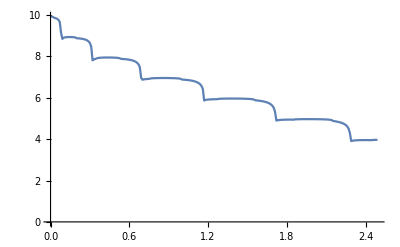

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,0,100,50,1]},{ω,Range[0,2.49,0.01]}]]
```

```mathematica
Clear[CA,ir,il]
```

```mathematica
Mean[ParallelTable[CA[1,0.0001,1,0,0,40,20,n],{n,750}]]
```

6.88092

```mathematica
Mean[ParallelTable[CA[ω,0.0001,1,0,1,40,20,n],{n,750}]]
```

4.09955

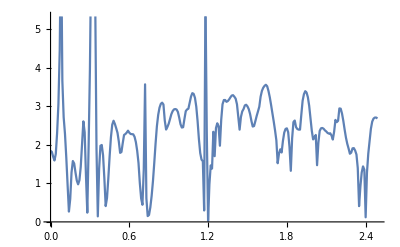

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,20,5,2]},{ω,Range[0,2.49,0.01]}]]
```

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/20*20/leads_1_20_and_1_10/up_down/half/60_ϵ1_conc_diag_"<>ToString[conc]<>"_.dat",Print[conc];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,60,conc,n],{n,500}]]},{ω,Range[0,2.49,0.01]}]],{conc,5,50,5}]
```

5

$Aborted

```mathematica
transmission = Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/20*20/leads_1_20_and_1_10/up_down/half/60_ϵ1_conc_diag_"<>ToString[x]<>"_.dat"]},{x,5,50,5}]
```

{{5,{{0.,3.63148},{0.01,3.75423},{0.02,3.53162},{0.03,3.09229},{0.04,2.90857},{0.05,2.85786},{0.06,2.37334},{0.07,2.21513},{0.08,4.8521},{0.09,3.91483},{0.1,3.35147},{0.11,3.4917},{0.12,3.70184},{0.13,3.90499},{0.14,4.15733},221,{2.36,2.88522},{2.37,2.91708},{2.38,2.93893},{2.39,2.98134},{2.4,3.01704},{2.41,3.04818},{2.42,3.05051},{2.43,3.07086},{2.44,3.06833},{2.45,3.01312},{2.46,2.96755},{2.47,2.98533},{2.48,2.94764},{2.49,3.00117}}},8,{50,{1}}}
 |  |  |  |

```mathematica
input= Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,60,15,n]},{ω,Range[0,2.49,0.01]}],{n,700,800}]
```

{{{0.,0.872592},{0.01,1.27859},{0.02,1.57488},{0.03,1.63436},{0.04,0.929153},{0.05,0.746074},{0.06,2.33811},{0.07,2.7429},{0.08,4.57006},{0.09,4.7367},{0.1,4.42296},{0.11,1.51627},{0.12,0.203631},{0.13,0.991754},{0.14,1.42746},221,{2.36,1.76295},{2.37,1.80787},{2.38,1.96465},{2.39,2.14493},{2.4,2.29976},{2.41,2.43825},{2.42,2.5562},{2.43,2.65725},{2.44,2.733},{2.45,2.82119},{2.46,2.93022},{2.47,2.99681},{2.48,3.01717},{2.49,3.02134}},99,{1}}
 |  |  |  |

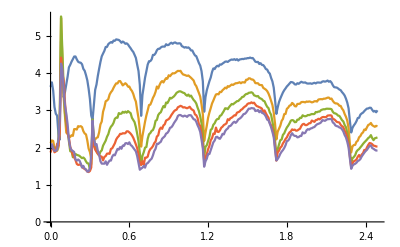

```mathematica
ListLinePlot[Table[transmission[[x,2]],{x,1,9,2}]]
```

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;250]][[;;,1]],(m5[[1;;250,2]]-transmission[[con,2]][[1;;250,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,10}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Abs[Table[misfit[2.49,0,x][[2]][[1]]-15,{x,100}]]/15//Mean//N
```

0.156667

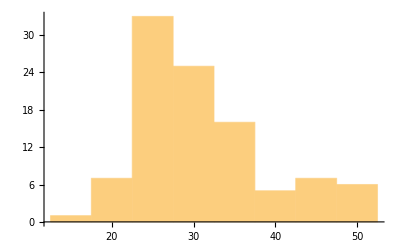

```mathematica
Histogram[%55]
```